```mathematica
ToString[x[1,4]]
```

x[1, 4]

```mathematica
InputForm[Characters["x[1, 4]"]]
```

{"x", "[", "1", ",", " ", "4", "]"}

```mathematica
x[1,4] /. x[i_,j_]-> {ToString[i],ToString[j]}
```

{i,j}

```mathematica
SetDirectory["~/maths/ibmer/papers/mdgp/intro_dg"]
```

/Users/liberti/maths/ibmer/papers/mdgp/intro_dg

```mathematica
Get["CayleyMenger.m"]
```

```mathematica
G=Graph[{1<->2,1<->3,2<->3,2<->4,3<->4},VertexLabels->"Name",EdgeWeight->{2,2,1,1,1}]
A=Normal[WeightedAdjacencyMatrix[G]]
```

-Graphics-

{{0,2,2,0},{2,0,1,1},{2,1,0,1},{0,1,1,0}}

```mathematica
y=Array[x,Dimensions[A]]
CMEq=CayleyMengerDeterminantSymbolic[A,y]
```

{{x[1,1],x[1,2],x[1,3],x[1,4]},{x[2,1],x[2,2],x[2,3],x[2,4]},{x[3,1],x[3,2],x[3,3],x[3,4]},{x[4,1],x[4,2],x[4,3],x[4,4]}}

-18+18 x[1,4]^2-2 x[1,4]^4

```mathematica
theVars = Union[Select[Level[CMEq, -1], MatchQ[#, x[i_,j_]]&]]
```

{x[1,4]}

```mathematica
CMEq
```

-18+18 x[1,4]^2-2 x[1,4]^4

```mathematica
Level[CMEq,{-2}]
```

{x[1,4],x[1,4]}

```mathematica
CMEq2 = -18 z+18 y[[1,4]]^2 - 2 y[[1,4]]^4
```

-18 z+18 x[1,4]^2-2 x[1,4]^4

```mathematica
Select[Level[CMEq2, {-2}], MatchQ[#, x[i_,j_]]& ]
```

{x[1,4],x[1,4]}

```mathematica
Solve[CMEq==0, theVars]
```

{{x[1,4]→-√(3/2 (3-√5))},{x[1,4]→√(3/2 (3-√5))},{x[1,4]→-√(3/2 (3+√5))},{x[1,4]→√(3/2 (3+√5))}}

```mathematica
Get["CayleyMenger.m"]
```

```mathematica
CayleyMengerVarsSymbolic[A, y]
```

{x[1,4]}

```mathematica
Map[x[First[#],Last[#]]&,CayleyMengerSymbolic[A,y]]
```

{x[1,4]}

```mathematica
Cases[Position[A,0], {i_,j_}/;i<j]
```

{{1,4}}

```mathematica
CayleyMengerVarsSymbolic[A, y] /.Solve[CayleyMengerDeterminantSymbolic[A, y]==0, CayleyMengerVarsSymbolic[A, y]]
```

{{-√(3/2 (3-√5))},{√(3/2 (3-√5))},{-√(3/2 (3+√5))},{√(3/2 (3+√5))}}

```mathematica
n = Length[VertexList[G]]
```

4

```mathematica
J=ConstantArray[1, {n,n}]
```

{{1,1,1,1},{1,1,1,1},{1,1,1,1},{1,1,1,1}}

```mathematica
H = IdentityMatrix[n] - J/n
```

{{3/4,-1/4,-1/4,-1/4},{-1/4,3/4,-1/4,-1/4},{-1/4,-1/4,3/4,-1/4},{-1/4,-1/4,-1/4,3/4}}

```mathematica
A
```

{{0,2,2,0},{2,0,1,1},{2,1,0,1},{0,1,1,0}}

```mathematica
M = -A*A / 2
```

{{0,-2,-2,0},{-2,0,-1/2,-1/2},{-2,-1/2,0,-1/2},{0,-1/2,-1/2,0}}

```mathematica
B= H.(-A*A/2).H
```

{{21/16,-15/16,-15/16,9/16},{-15/16,13/16,5/16,-3/16},{-15/16,5/16,13/16,-3/16},{9/16,-3/16,-3/16,-3/16}}

```mathematica
λ = Eigenvalues[B]
```

{3/8 (3+√17),1/2,3/8 (3-√17),0}

```mathematica
p = Count[λ, x_ /; x>0]
```

2

```mathematica
V = Take[Eigenvectors[B], p]
```

{{1/2 (3+√17),1/4 (-5-√17),1/4 (-5-√17),1},{0,-1,1,0}}

```mathematica
P = Take[Sqrt[λ], p]*V
```

{{1/4 √(3/2) (3+√17)^(3/2),1/8 (-5-√17) √(3/2 (3+√17)),1/8 (-5-√17) √(3/2 (3+√17)),1/2 √(3/2 (3+√17))},{0,-1/(√2),1/(√2),0}}

```mathematica
N[Transpose[P].P]
```

{{33.8828,-21.6982,-21.6982,9.51349},{-21.6982,14.3952,13.3952,-6.09233},{-21.6982,13.3952,14.3952,-6.09233},{9.51349,-6.09233,-6.09233,2.67116}}

```mathematica
N[B]
```

{{1.3125,-0.9375,-0.9375,0.5625},{-0.9375,0.8125,0.3125,-0.1875},{-0.9375,0.3125,0.8125,-0.1875},{0.5625,-0.1875,-0.1875,-0.1875}}

```mathematica
N[Transpose[P]]
```

{{5.82089,0.},{-3.72763,-0.707107},{-3.72763,0.707107},{1.63437,0.}}

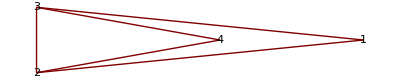

```mathematica
GraphPlot[G, VertexLabeling-> True, VertexCoordinateRules->Transpose[P]]
```

```mathematica
Get["DGPSystem.m"];
```

```mathematica
K=2
```

2

```mathematica
myVars=Array[x,{Length[VertexList[G]],K}];
S=DGPSystemSquaredVars[G,K,myVars]
```

{(x[1,1]-x[2,1])^2+(x[1,2]-x[2,2])^2==4,(x[1,1]-x[3,1])^2+(x[1,2]-x[3,2])^2==4,(x[2,1]-x[3,1])^2+(x[2,2]-x[3,2])^2==1,(x[2,1]-x[4,1])^2+(x[2,2]-x[4,2])^2==1,(x[3,1]-x[4,1])^2+(x[3,2]-x[4,2])^2==1}

```mathematica
IncongruentSolutions={x[1,1]->0,x[1,2]->0,x[2,1]->2, x[2,2]->0};
SI=S/.IncongruentSolutions
```

{True,x[3,1]^2+x[3,2]^2==4,(2-x[3,1])^2+x[3,2]^2==1,(2-x[4,1])^2+x[4,2]^2==1,(x[3,1]-x[4,1])^2+(x[3,2]-x[4,2])^2==1}

```mathematica
sol=Solve[Apply[And,SI],Flatten[myVars],Reals]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{x[3,1]→7/4,x[3,2]→-(√15)/4,x[4,1]→1/8 (15-3 √5),x[4,2]→-(15-3 √5)/(8 √15)},{x[3,1]→7/4,x[3,2]→-(√15)/4,x[4,1]→1/8 (15+3 √5),x[4,2]→-(15+3 √5)/(8 √15)},{x[3,1]→7/4,x[3,2]→(√15)/4,x[4,1]→1/8 (15-3 √5),x[4,2]→(15-3 √5)/(8 √15)},{x[3,1]→7/4,x[3,2]→(√15)/4,x[4,1]→1/8 (15+3 √5),x[4,2]→(15+3 √5)/(8 √15)}}

```mathematica
sol2=myVars/.IncongruentSolutions/.sol
```

{{{0,0},{2,0},{7/4,-(√15)/4},{1/8 (15-3 √5),-(15-3 √5)/(8 √15)}},{{0,0},{2,0},{7/4,-(√15)/4},{1/8 (15+3 √5),-(15+3 √5)/(8 √15)}},{{0,0},{2,0},{7/4,(√15)/4},{1/8 (15-3 √5),(15-3 √5)/(8 √15)}},{{0,0},{2,0},{7/4,(√15)/4},{1/8 (15+3 √5),(15+3 √5)/(8 √15)}}}

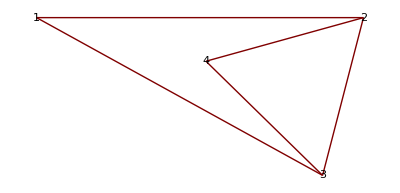
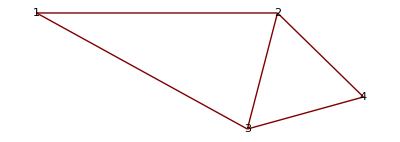
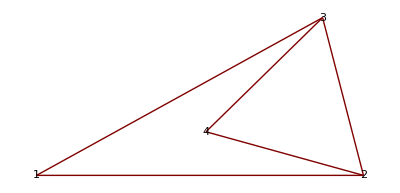
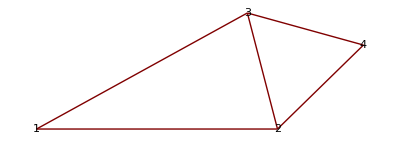

```mathematica
Map[GraphPlot[G,VertexLabeling->True,VertexCoordinateRules->#]&,sol2]
```

```mathematica
G1 =RandomGraph[{10, 30}, EdgeWeight-> RandomSample[Range[5], 30]]
```

RandomSample::smplen: RandomSample cannot generate a sample of length 30, which is greater than the length of the sample set {1, 2, 3, 4, 5}. If you want a choice of possibly repeated elements from the set, use RandomChoice.

```mathematica
G1=RandomGraph[{10,30},EdgeWeight->RandomInteger[5,30]]
```

-Graphics-

```mathematica
RandomInteger[5, 30]
```

{5,2,2,4,1,2,0,4,0,3,2,0,3,3,5,3,2,0,3,0,2,2,1,0,0,3,2,4,2,1}

```mathematica
Get["ApproxRealize.m"]
```

```mathematica
x= ApproxRealizeGraph[G1]
```

{{0.317975,-0.207132,-0.151121,0.0288158,-2.39591,-0.244705},{-0.524303,0.898762,-0.398074,0.019112,-0.143452,0.176435},{0.672683,-0.279732,0.0393369,-0.0385133,2.07677,0.218697},{-0.601949,-0.835432,0.205027,0.000120357,-1.36097,0.282273},{1.52543,0.456145,0.350664,-0.0528907,-0.259676,-0.136653},{-1.3231,0.509765,0.364023,-0.0180012,0.108456,-0.0441554},{-0.654503,-0.454539,-0.0859522,0.0487052,1.89185,-0.366831},{-0.44833,-0.0709669,-0.158938,-0.148775,-0.194966,-0.0504254},{0.810035,-0.213157,-0.354809,0.0212113,0.167801,0.0737488},{0.226059,0.196288,0.189844,0.140215,0.110104,0.091615}}

```mathematica
l1 = Map[(EuclideanDistance[x[[First[#]]], x[[Last[#]]]])&, Tuples[Range[n], 2]]
```

{0.,2.69155,4.5157,1.64848,2.59452,3.12837,4.40584,2.34931,2.63775,2.5871,2.69155,0.,2.81912,2.20706,2.2527,1.21806,2.52671,1.04194,1.76808,1.21996,4.5157,2.81912,0.,3.71275,2.63649,2.94204,1.48065,2.56611,1.96147,2.08916,1.64848,2.20706,3.71275,0.,2.75795,2.14965,3.35217,1.49429,2.25287,1.99257,2.59452,2.2527,2.63649,2.75795,0.,2.87445,3.23488,2.11047,1.29998,1.417,3.12837,1.21806,2.94204,2.14965,2.87445,0.,2.20646,1.21867,2.36824,1.60373,4.40584,2.52671,1.48065,3.35217,3.23488,2.20646,0.,2.16538,2.33295,2.1606,2.34931,1.04194,2.56611,1.49429,2.11047,1.21867,2.16538,0.,1.34832,0.919039,2.63775,1.76808,1.96147,2.25287,1.29998,2.36824,2.33295,1.34832,0.,0.907266,2.5871,1.21996,2.08916,1.99257,1.417,1.60373,2.1606,0.919039,0.907266,0.}

```mathematica
l2 = Flatten[Normal[WeightedAdjacencyMatrix[G1]]]
```

{0,2,3,0,2,4,0,0,0,0,2,0,3,5,5,0,4,0,0,1,3,3,0,1,0,4,1,0,0,0,0,5,1,0,5,0,3,0,2,0,2,5,0,5,0,3,5,3,2,0,4,0,4,0,3,0,0,0,5,0,0,4,1,3,5,0,0,0,0,0,0,0,0,0,3,0,0,0,0,4,0,0,0,2,2,5,0,0,0,0,0,1,0,0,0,0,0,4,0,0}

```mathematica
mm = Mean[Flatten[Map[(l1[[#]]/l2[[#]])&, Position[l2, x_/;x>0]]]]
```

19.0614

```mathematica
RandomReal[Max[Abs[x]], {4, 2}]
```

{{1.52542,1.15469},{0.591316,0.231998},{0.947322,0.61101},{2.2438,0.226326}}

```mathematica
RandomChoice[Select[Tuples[Range[n],2],(WeightedAdjacencyMatrix[G1][[First[#], Last[#]]]>0)&]]
```

{5,7}

```mathematica
Accuracy[0.0001]
```

19.9546

```mathematica
Select[Flatten[Normal[WeightedAdjacencyMatrix[G1]]], Positive]
```

{2,3,2,4,2,3,5,5,4,1,3,3,1,4,1,5,1,5,3,2,2,5,5,3,5,3,2,4,4,3,5,4,1,3,5,3,4,2,2,5,1,4}

```mathematica
x = StochasticProximityEmbedding[G, 2]
```

```mathematica
G
```

-Graphics-

```mathematica
Normal[WeightedAdjacencyMatrix[G]]
```

{{0,2,2,0},{2,0,1,1},{2,1,0,1},{0,1,1,0}}

```mathematica
x
```

x

```mathematica
1+1
```

2